```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
SetDirectory["../../figs/"]
```

/Users/novakm/Git/FR_n-prey-at-a-time/code/mathematica

/Users/novakm/Git/FR_n-prey-at-a-time/figs

```mathematica
f[n_,ϕ_,R_]=(a R^ϕ (-1+(a h R^ϕ)^n))/(-1+(a h R^ϕ)^(1+n));
finf[R_]=a R;
```

```mathematica
fparms={h-> 4,a-> 0.1};
nvals={1,20};
ϕvals = {1,2};
```

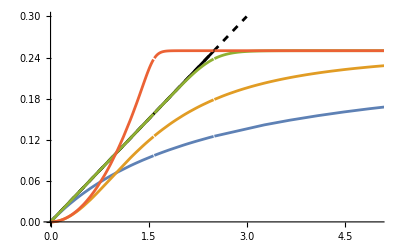

```mathematica
prange = {{0,5},{0,0.3}};
p1=Plot[Evaluate[f[n,ϕ,R]/.fparms/.n-> nvals/.ϕ->ϕvals], {R,0,20},
PlotRange->prange
];
p2a=Plot[finf[R]/.fparms,{R,0,20},
PlotRange->prange,
PlotStyle->{Black,Dashed}];
p2b=Plot[finf[R]/.fparms,{R,0,1/(a h)/.fparms},
PlotRange->prange,
PlotStyle->{Black}];
P1=Show[p2b,p2a,p1]
(* Export["FR_n-prey-at-a-time-General.pdf",P1,"PDF",
"AllowRasterization"->False,ImageSize->360];*)
```